```mathematica
(*Parameters*)
cmks=299792458;
lambda= 1053*^-9;
omega1 = 2 * Pi * cmks/lambda;
omega2 = 4*Pi*cmks/lambda;
(*Indeces of refraction*)
no1 = 1.655;
no2 =1.675;

K1 = (2*(120*Pi/no1)^3*omega1^2*(17.1*^-24/Sqrt[2])^2);K2 = (2*(120*Pi/no2)^3*omega2^2*(17.1*^-24/Sqrt[2])^2);
(*Infra red energy and pulse duration sigma*)
Eir=1.5*^-3;
sigmat = 2.2*^-12;
(*Phase mismatch*)
dk1 =1*^-3;
dk2 =3*^-2;
(*Grid size*)
Nx=21;
Ny=21;
Lx =5.25*^-3;
Ly =5.25*^-3;
delx =(Lx/Nx);
dely =(Ly/Ny);
wx =2.0*^-3;
wy =2.0*^-3;
l = 2.0*^-3;
Nt= 401;
tRange = 8;
dt =2.*tRange/(Nt-1);
dA = delx*dely;
Pmax =Eir/(Sqrt[(2*Pi)]*sigmat);
mmf1 =Sin[dk1*l/2]/(dk1*l/2);
mmf2 =Sin[(dk2*l/2)]/(dk2*l/2);
Eirf0 = 2*Eir/(Pi*wx*wy);
EirTot = 0.;
EgrTot = 0.;
EuvTot = 0.;
counter = 0;
```

```mathematica
t=Table[i,{i,-tRange,tRange,2* tRange/Nt}]//N;
```

```mathematica
Pd1 = ConstantArray[c,{Nx-1,Ny-1}];
Pd2 = ConstantArray[c,{Nx-1,Ny-1}];
Pd4 = ConstantArray[c,{Nx-1,Ny-1}];
```

```mathematica
For[i=1,i<Nx,i++,
x =(i-1-(Nx-1)/2)*delx;
For[j =1,j<Ny,j++,
y=(j-1-(Ny-1)/2)*dely;
expArgSp =-(2*(x/wx)^2+2*(y/wy)^2);
Eirf = Eirf0*E^(expArgSp);
EirIJ=(Eirf*dA);
EirTot=(EirTot+EirIJ);
Pd1[[i,j]]=Eirf/(Sqrt[2*Pi] * sigmat) * Exp[-(t*1*^-12)^2/(2*sigmat^2)];
Pd2[[i,j]]= Tanh[l * Sqrt[K1]*Sqrt[Pd1[[i,j]]]* mmf1]^2 * Pd1[[i,j]];
 Pd4 [[i,j]]= Tanh[l*Sqrt[K2] * Sqrt[Pd2[[i,j]]]*mmf2]^2 Pd2[[i,j]];
(*Power as a function of time for each spatial point*)
]
]
```

```mathematica
Eirl = ConstantArray[c,{Nx-1,Ny-1}];
Egr = ConstantArray[c,{Nx-1,Ny-1}];
Euv = ConstantArray[c,{Nx-1,Ny-1}];

For[i=1,i<Nx,i++,
x =(i-1-(Nx-1)/2)*delx;
For[j =1,j<Ny,j++,
y=(j-1-(Ny-1)/2)*dely;
expArgSp =-(2*(x/wx)^2+2*(y/wy)^2);
Eirf = Eirf0*E^(expArgSp);
EirIJ=(Eirf*dA);
EirTot=(EirTot+EirIJ);
Eirl[[i,j]] = NIntegrate[Interpolation[{t,Pd1[[i,j]]}//Transpose][t1],{t1,-tRange,tRange}]  *dA*1*^-12;
Egr[[i,j]] = NIntegrate[Interpolation[{t,Pd2[[i,j]]}//Transpose][t1],{t1,-tRange,tRange}]  *dA*1*^-12;
Euv[[i,j]] = NIntegrate[Interpolation[{t,Pd4[[i,j]]}//Transpose][t1],{t1,-tRange,tRange}]  *dA*1*^-12;

(*Energy from power density integration*)
]
]
```

```mathematica
(*ListPlot [{t,Pd1[[11,11]]}//Transpose]
d =Interpolation[{t,Pd1[[1,9]]}//Transpose]
Integrate[d[t1],{t1,-tRange,tRange}]*)
```

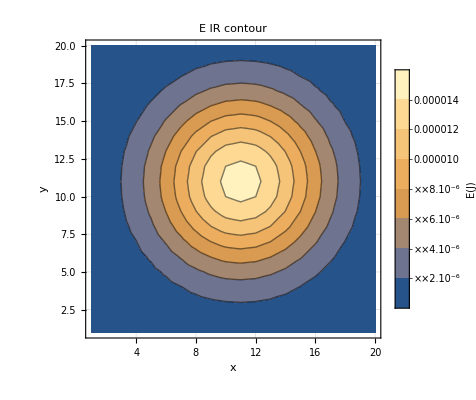

```mathematica
ListContourPlot[Eirl,PlotRange->All,GridLines->True,FrameLabel->{"x","y"},PlotLegends ->BarLegend[Automatic,LegendLabel-> "E(J)"],PlotLabel->"E IR contour"]
```

```mathematica
ListPlot3D[Eirl,PlotRange->All,PlotLabel->"E IR",ColorFunction->"Rainbow",ImageSize->Large]
```

-Graphics3D-

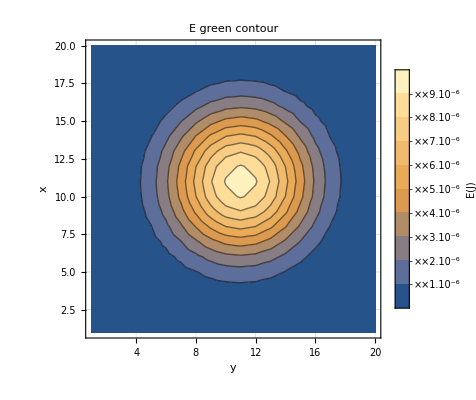

```mathematica
ListContourPlot[Egr,PlotRange->All,GridLines->True,FrameLabel->{"y","x"},PlotLegends ->BarLegend[Automatic,LegendLabel-> "E(J)"],PlotLabel->"E green contour"]
```

```mathematica
ListPlot3D[Egr,PlotRange->All,PlotLabel->"E green",ColorFunction->"Rainbow",ImageSize->Large]
```

-Graphics3D-

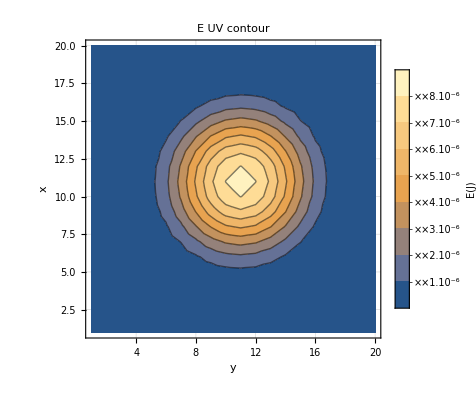

```mathematica
ListContourPlot[Euv,PlotRange->All,GridLines->True,FrameLabel->{"y","x"},PlotLegends ->BarLegend[Automatic,LegendLabel-> "E(J)"],PlotLabel->"E UV contour"]
```

```mathematica
Euv;
```

```mathematica
ListPlot3D[Euv,PlotRange->All,PlotLabel->"E UV",ColorFunction->"Rainbow",ImageSize->Large]
```

-Graphics3D-

#### Total energy and conversion efficiency calculation

```mathematica
EirTot;
```

```mathematica
Eirtot =Total[Total[Eirl]]
```

0.00146122

```mathematica
Egrtot =Total[Total[Egr]]
```

0.000599754

```mathematica
Euvtot =Total[Total[Euv]]
```

0.000417322

```mathematica
ceffir2gr = Egrtot/Eirtot
```

0.410447

```mathematica
ceffgr2uv =Euvtot / Egrtot
```

0.695822

```mathematica
ceffir2uv = Euvtot/Eirtot
```

0.285598

```mathematica
Insert[Grid[{{"Eir","Egr","Euv"},{Eirtot,Egrtot,Euvtot}}],{Background->{None,{GrayLevel[0.7],{White}}},Dividers->{Black,{2->Black}},Frame->True,Spacings->{2,{2,{0.7},2}}},2]
```

Eir | Egr | Euv
0.00146122 | 0.000599754 | 0.000417322

```mathematica
Insert[Grid[{{"ir2gr","gr2uv","ir2uv"},{ceffir2gr,ceffgr2uv,ceffir2uv}}],{Background->{None,{GrayLevel[0.7],{White}}},Dividers->{Black,{2->Black}},Frame->True,Spacings->{2,{2,{0.7},2}}},2]
```

ir2gr | gr2uv | ir2uv
0.410447 | 0.695822 | 0.285598

### Calculation of Pulse Length

```mathematica
Pir ={t,Pd1[[11,11]]*1*^-9/1*^4}//Transpose;
Pgreen  ={t,Pd2[[11,11]]*1*^-9/1*^4}//Transpose;
Puv ={t,Pd4[[11,11]]*1*^-9/1*^4}//Transpose;
```

Pd vs time IR

{A→4.32911,σ→2.2}

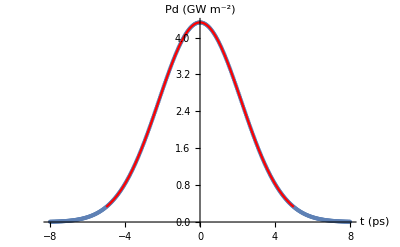

```mathematica
model[time_]= A*Exp[-(1/2) ((time)/σ)^2];
fit1= FindFit[Pir,model[time],{ A, σ},time,MaxIterations->1000000]
Show[ListPlot[Pir,PlotStyle->Thick,PlotRange->All],Plot[model[x]/.fit1,{x,-5,5},PlotStyle->Red],AxesLabel->{"t (ps)","Pd (GW m^-2)"},LabelStyle->{GrayLevel[0]}]
```

Pd vs time green

{A→3.40657,σ→1.79834}

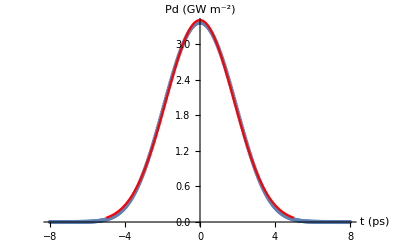

```mathematica
fit2= FindFit[Pgreen,model[time],{ A, σ},time,MaxIterations->10000]
Show[ListPlot[Pgreen,PlotStyle->Thick,PlotRange->All],Plot[model[x]/.fit2,{x,-5,5},PlotStyle->Red,PlotRange->All],AxesLabel->{"t (ps)","Pd (GW m^-2)"},LabelStyle->{GrayLevel[0]}]
```

Pd vs time UV

{A→3.33674,σ→1.6458}

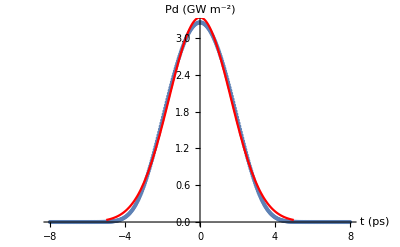

```mathematica
fit3= FindFit[Puv,model[time],{ A, σ},time,MaxIterations->10000]
Show[ListPlot[Puv,PlotStyle->Thick,PlotRange->All],Plot[model[x]/.fit3,{x,-5,5},PlotStyle->Red,PlotRange->All],AxesLabel->{"t (ps)","Pd (GW m^-2)"},LabelStyle->{GrayLevel[0]}]
```

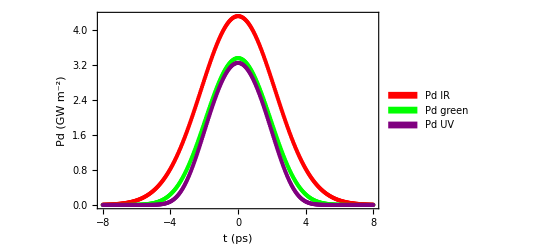

```mathematica
p1 =ListPlot[Pir,PlotStyle->Red,PlotRange->All,Frame-> True,FrameLabel->{"t (ps)","Pd (GW m^-2)"},LabelStyle->{GrayLevel[0]}];
p2=ListPlot[Pgreen,PlotStyle->Green,Frame-> All,PlotRange->All];
p3=ListPlot[Puv,PlotStyle->Purple,PlotRange->All,Frame-> All];
Legended[Show[p1,p2,p3],SwatchLegend[{Red,Green,Purple},{"Pd IR","Pd green","Pd UV"}]]
```

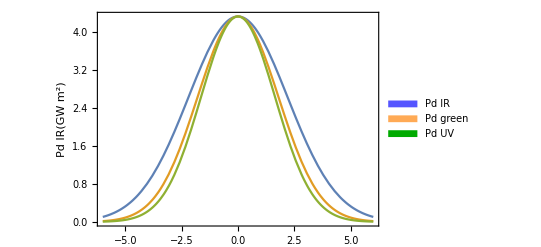

```mathematica
Clear[threeyaxisplot];
threeyaxisplot[{f1_,f1label_},{f2_,f2label_},{f3_,f3label_},range:{var_Symbol,vmin_?NumericQ,vmax_?NumericQ}]:=Module[{plot1,plot2,plot3,p1yrng,p2yrng,p3yrng,p2yaxis,p3yaxis},{{plot1,plot2,plot3}=Plot[#[var],range,Axes->False,Frame->{True,True,False,False},PlotRangeClipping->False]&/@{f1,f2,f3}};
{p2yaxis,p3yaxis}=Plot[(First@#)[var],range,Axes->False,Frame->{False,True,False,False},PlotStyle->White,FrameLabel->{None,Last@#}]&/@{{f2,f2label},{f3,f3label}};
{p1yrng,p2yrng,p3yrng}=Last@(PlotRange/.Options[#,PlotRange])&/@{plot1,plot2,plot3};
Plot[{f1[var],Rescale[f2[var],p2yrng,p1yrng],Rescale[f3[var],p3yrng,p1yrng]},range,PlotRangeClipping->False,Axes->False,Frame->{True,True,False,False},FrameLabel->{None,f1label},Epilog->{Inset[p2yaxis,Scaled@{1.6,0.5},Scaled@{0.5,0.5},Scaled@1.07],Inset[p3yaxis,Scaled@{1.85,0.5},Scaled@{0.5,0.5},Scaled@1.07]},ImagePadding->{{Automatic,130},{Automatic,Automatic}}]]
out=Legended[threeyaxisplot[{model[#]/.fit1 &,"Pd IR(GW m^2)"},{model[#]/.fit2 &,"Pd green"},{model[#]/.fit3 &,"Pd UV"},{x1,-6,6}],SwatchLegend[{Lighter[Blue],Lighter[Orange],Darker[Green]},{"Pd IR","Pd green","Pd UV"},LegendMarkerSize->8,LabelStyle->{FontSize->10}]]
```

Adapted from code by Jeff Dooling, Accelerator System Division, Advanced Photon Source, 

#!/bin/sh
# \
exec oagtclsh “$0” “$@”
#
set auto_path [linsert $auto_path 0 /usr/local/oag/apps/lib/$env(HOST_ARCH)]
set auto_path [linsert $auto_path 0 /usr/local/oag/lib_patch/$env(HOST_ARCH)]
package require sdds
#
# Calculate the HHG temporal and spatial widths and conversion efficiencies.
# Using mks units (where practical, e.g. using ps rather than s is an example
# where it’s not).
#
set pi [expr (4.*atan(1))]
set c_mks 299792458.
set lambda_1 1053e-9
set omega_1 [expr 2.*$pi*$c_mks/$lambda_1]
set omega_2 [expr 4.*$pi*$c_mks/$lambda_1]
set n_o1 1.655
set n_o2 1.675
set K1 [expr (2*(120*$pi/$n_o1)**3*$omega_1**2*(17.1e-24/sqrt(2))**2)]
set K2 [expr (2*(120*$pi/$n_o2)**3*$omega_2**2*(17.1e-24/sqrt(2))**2)]
set Eir 1.5e-3
set sigma_t 2.5e-12
set d_k1 1e-3
set d_k2 3e-2
set Nx 21
set Ny 21
set Lx 5.25e-3
set Ly 5.25e-3
set del_x [expr ($Lx/$Nx)]
set del_y [expr ($Ly/$Ny)]
set w_x 2.0e-3
set w_y 2.0e-3
set l 1.0e-3
set Nt 401
set tRange 8.0
set dt [expr (2.*$tRange/($Nt-1))]
set dA [expr ($del_x*$del_y)]
set Pmax [expr ($Eir/(sqrt(2*$pi)*$sigma_t))]
set mmf1 [expr ((sin($d_k1*$l/2))/($d_k1*$l/2))]
set mmf2 [expr ((sin($d_k2*$l/2))/($d_k2*$l/2))]
set Eirf0 [expr 2*$Eir/($pi*$w_x*$w_y)]
set EirTot 0.
set EgrTot 0.
set EuvTot 0.
set counter 0

puts stdout “Pmax = $Pmax W, Eirf0 = $Eirf0 J/m^2, K1 = $K1 1/W, K2 = $K2 1/W, mmf1 = $mmf1, mmf2 = $mmf2”
puts stdout “del_x = $del_x m, del_y = $del_y m, dt = $dt ps”
#exit

for {set i 0} {$i<$Nx} {incr i} {
   set x [expr {($i - ($Nx -1)/2) * $del_x}]
   for {set j 0} {$j<$Ny} {incr j} {
      set y [expr {($j - ($Ny -1)/2) * $del_y}]
      set expArgSp [expr -(2*($x/$w_x)**2 + 2*($y/$w_y)**2)] 
      set Eirf [expr $Eirf0*exp($expArgSp)]
      set EirIJ [expr ($Eirf*$dA)]
      set EirTot [expr ($EirTot+$EirIJ)]
#      puts -nonewline stdout “i = $i, j = $j “  
#      puts stdout “i = $i, x = $x m, j = $j, y = $y m, EirIJ = $EirIJ J”  
      if {$i==0 && $j==0} {exec sddssequence -pipe=out -define=t,type=double,units=ps \
      -sequence=begin=-$tRange.,number=$Nt,end=$tRange.\
      | sddsprocess -pipe=in pulseIR.txySeq \
      “-define=col,Pir,$Eir 2 $pi * sqrt $sigma_t * / t 1e-12 * sqr $sigma_t sqr -2 * / exp *,type=double,units=W” \
      “-define=col,Pd1${i}_${j},$Eirf 2 $pi * sqrt $sigma_t * / t sqr $sigma_t 1e12 * sqr -2 * / exp *,type=double,units=Wm\$a-2\$n” \
      “-define=col,Pd2${i}_${j},$l $K1 sqrt * Pd1${i}_${j} sqrt * $mmf1 * tanh sqr Pd1${i}_${j} *,type=double,units=Wm\$a-2\$n” \
      “-define=col,Pd4${i}_${j},$l $K2 sqrt * Pd2${i}_${j} sqrt * $mmf2 * tanh sqr Pd2${i}_${j} *,type=double,units=Wm\$a-2\$n” \
      -process=Pd1${i}_${j},gmintegral,EirInt${i}_${j},functionOf=t \
      -process=Pd2${i}_${j},gmintegral,EgrInt${i}_${j},functionOf=t \
      -process=Pd4${i}_${j},gmintegral,EuvInt${i}_${j},functionOf=t \
      “-define=par,Eir${i}_${j},EirInt${i}_${j} $dA * 1e-12 *,type=double,units=J” \
      “-define=par,Egr${i}_${j},EgrInt${i}_${j} $dA * 1e-12 *,type=double,units=J” \
      “-define=par,Euv${i}_${j},EuvInt${i}_${j} $dA * 1e-12 *,type=double,units=J” 
      } else {exec sddsprocess pulseIR.txySeq -nowarn \
      “-define=col,Pd1${i}_${j},$Eirf 2 $pi * sqrt $sigma_t * / t sqr $sigma_t 1e12 * sqr -2 * / exp *,type=double,units=Wm\$a-2\$n” \
      “-define=col,Pd2${i}_${j},$l $K1 sqrt * Pd1${i}_${j} sqrt * $mmf1 * tanh sqr Pd1${i}_${j} *,type=double,units=GWcm\$a-2\$n” \
      “-define=col,Pd4${i}_${j},$l $K2 sqrt * Pd2${i}_${j} sqrt * $mmf2 * tanh sqr Pd2${i}_${j} *,type=double,units=GWcm\$a-2\$n” \
      -process=Pd1${i}_${j},gmintegral,EirInt${i}_${j},functionOf=t \
      -process=Pd2${i}_${j},gmintegral,EgrInt${i}_${j},functionOf=t \
      -process=Pd4${i}_${j},gmintegral,EuvInt${i}_${j},functionOf=t \
      “-define=par,Eir${i}_${j},EirInt${i}_${j} $dA * 1e-12 *,type=double,units=J” \
      “-define=par,Egr${i}_${j},EgrInt${i}_${j} $dA * 1e-12 *,type=double,units=J” \
      “-define=par,Euv${i}_${j},EuvInt${i}_${j} $dA * 1e-12 *,type=double,units=J” 
      }
   }
}
sdds load pulseIR.txySeq data

lappend output(ColumnNames) “Index”
set output(ColumnInfo.Index) “type SDDS_LONG”
for {set j 0} {$j<$Ny} {incr j} {
    lappend values $j
}
set output(Column.Index) [list $values]

for {set i 0} {$i<$Nx} {incr i} {
    lappend output(ColumnNames) Eir${i}
    set values “”
    for {set j 0} {$j<$Ny} {incr j} {
        lappend values [set data(Parameter.Eir${i}_${j})]
    }
    set output(Column.Eir${i}) [list $values]
    set output(ColumnInfo.Eir${i}) “type SDDS_DOUBLE”
}
for {set i 0} {$i<$Nx} {incr i} {
    lappend output(ColumnNames) Egr${i}
    set values “”
    for {set j 0} {$j<$Ny} {incr j} {
        lappend values [set data(Parameter.Egr${i}_${j})]
    }
    set output(Column.Egr${i}) [list $values]
    set output(ColumnInfo.Egr${i}) “type SDDS_DOUBLE”
}
for {set i 0} {$i<$Nx} {incr i} {
    lappend output(ColumnNames) Euv${i}
    set values “”
    for {set j 0} {$j<$Ny} {incr j} {
        lappend values [set data(Parameter.Euv${i}_${j})]
    }
    set output(Column.Euv${i}) [list $values]
    set output(ColumnInfo.Euv${i}) “type SDDS_DOUBLE”
}
sdds save pulseIR.E output

puts stdout “Eir_Tot = $EirTot J, Egr_Tot = $EgrTot J, Euv_Tot = $EuvTot J”
exit

```mathematica
CloudDeploy[Notebook["SHGxyIRwIR.nb'"],Permissions->"Public"]
```

CloudObject[]